```mathematica
d=Import["C:\\Users\\joshf\\OneDrive\\Documents\\D.dat","Data"];
```

```mathematica
w=Import["C:\\Users\\joshf\\OneDrive\\Documents\\W.dat","Data"];
```

```mathematica
x=Transpose[{Cases[Flatten[UpperTriangularize[w,1]],Except[0.]]}];
```

```mathematica
y=Transpose[{Cases[Flatten[UpperTriangularize[d,1]-LowerTriangularize[ConstantArray[η,{100,100}]]],Except[-η]]}];
```

```mathematica
data=Table[{x[[i,1]],y[[i,1]]},{i,1,4950}];
```

```mathematica
SeedRandom[2];sample=RandomSample[data,3960];
```

```mathematica
Dimensions[sample]
```

{3960,2}

```mathematica
logit=LogitModelFit[data,z,z]
```

FittedModel[1/(1+ⅇ^(«18»+«18» z))]

```mathematica
Normal[logit]
```

1/(1+ⅇ^(3.04662+0.752281 z))

```mathematica
f[z_]:=1/(1+ⅇ^(3.046617606045864+0.752281042745162 z))
```

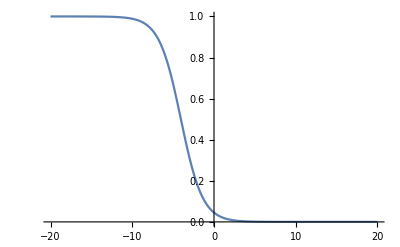

```mathematica
Plot[f[z],{z,-20,20}]
```

```mathematica
c=Classify[sample⟦All,1⟧->sample⟦All,2⟧,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Numerical
Classes | ,,01
Method | LogisticRegression
Accuracy | 95.3 % ± 2.9 %
Loss | 0.0045 ± 0.24
Single evaluation time | 1.06 ms/example
Batch evaluation speed | 617. examples/ms
Classifier memory | 332. kB
Training examples used | 3960 examples
Training time | 4.22 s
 |

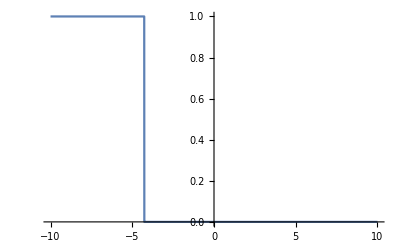

```mathematica
Plot[c[k],{k,-10,10}]
```